# AM radio

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

```mathematica
makeTemplate["Circuit 1","p1"]
```

## Circuit 1

```mathematica
With[{context="p1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
diffeqs={c vc'[t]==(vi[t]+vc[t])/r-il[t],
l il'[t]==vc[t]};
initialConds={vc[_?NumberQ]->0,il[_?NumberQ]->0}
Column[diffeqs,Frame->All]
lap=LaplaceTransform[#,t,s]&/@diffeqs;
Column[TraditionalForm/@lap,Frame->All]
lap2=lap/.initialConds;
Column[TraditionalForm/@lap2,Frame->All]
```

{vc[_?NumberQ]→0,il[_?NumberQ]→0}

c vc'[t]==-il[t]+(vc[t]+vi[t])/r
l il'[t]==vc[t]

c (s (ℒ_t[vc(t)](s))-vc(0))==-(ℒ_t[il(t)](s))+(ℒ_t[vc(t)](s))/r+(ℒ_t[vi(t)](s))/r
l (s (ℒ_t[il(t)](s))-il(0))==ℒ_t[vc(t)](s)

c s (ℒ_t[vc(t)](s))==-(ℒ_t[il(t)](s))+(ℒ_t[vc(t)](s))/r+(ℒ_t[vi(t)](s))/r
l s (ℒ_t[il(t)](s))==ℒ_t[vc(t)](s)

```mathematica
(lap3=Eliminate[lap2,il[t]])//TraditionalForm
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

l s (ℒ_t[vi(t)](s))==(c l r s^2-l s+r) (ℒ_t[vc(t)](s))∧r≠0

```mathematica
Solve[l s (Subscript[ℒ, t][vi(t)](s))==(c l r s^2-l s+r) (Subscript[ℒ, t][vc(t)](s))∧r≠0,Subscript[ℒ, t][vc(t)](s)]
```

{{LaplaceTransform[vc[t],t,s]→(l s LaplaceTransform[vi[t],t,s])/(r-l s+c l r s^2)}}

```mathematica
lap4=(l s)/(r-l s+c l r s^2);
Roots[Denominator[lap4]==0,s]
```

s==(l-√(l^2-4 c l r^2))/(2 c l r)||s==(l+√(l^2-4 c l r^2))/(2 c l r)

```mathematica
initial2={vc[0]==0,il[0]==0};
sol1=Simplify@DSolve[{diffeqs},{vc,il},t];
```

```mathematica
Column[TraditionalForm/@sol1,Frame->All]
```

{il→({t}↦1/(2 √(l (l-4 c r^2)))(ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r)) l-ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r)) l+ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r)) √(l (l-4 c r^2))+ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r)) √(l (l-4 c r^2))) c_1-(c (ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r))-ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r))) r c_2)/(√(l (l-4 c r^2)))+1/(2 √(l (l-4 c r^2)))(ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r)) l-ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r)) l+ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r)) √(l (l-4 c r^2))+ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r)) √(l (l-4 c r^2))) Integrate[-((ⅇ^(-((l-√(l (l-4 c r^2))) K[1])/(2 c l r))-ⅇ^(-((l+√(l (l-4 c r^2))) K[1])/(2 c l r))) vi(K[1]))/(√(l (l-4 c r^2))),{K[1],1,t},Assumptions→True]-1/(√(l (l-4 c r^2)))c (ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r))-ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r))) r Integrate[1/(2 c r √(l (l-4 c r^2)))(-ⅇ^(-((l-√(l (l-4 c r^2))) K[2])/(2 c l r)) l+ⅇ^(-((l+√(l (l-4 c r^2))) K[2])/(2 c l r)) l+ⅇ^(-((l-√(l (l-4 c r^2))) K[2])/(2 c l r)) √(l (l-4 c r^2))+ⅇ^(-((l+√(l (l-4 c r^2))) K[2])/(2 c l r)) √(l (l-4 c r^2))) vi(K[2]),{K[2],1,t},Assumptions→True]),vc→({t}↦((ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r))-ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r))) l r c_1)/(√(l (l-4 c r^2)))+1/(2 √(l (l-4 c r^2)))(-ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r)) l+ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r)) l+ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r)) √(l (l-4 c r^2))+ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r)) √(l (l-4 c r^2))) c_2+1/(√(l (l-4 c r^2)))(ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r))-ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r))) l r Integrate[-((ⅇ^(-((l-√(l (l-4 c r^2))) K[1])/(2 c l r))-ⅇ^(-((l+√(l (l-4 c r^2))) K[1])/(2 c l r))) vi(K[1]))/(√(l (l-4 c r^2))),{K[1],1,t},Assumptions→True]+1/(2 √(l (l-4 c r^2)))(-ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r)) l+ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r)) l+ⅇ^(((l-√(l (l-4 c r^2))) t)/(2 c l r)) √(l (l-4 c r^2))+ⅇ^(((l+√(l (l-4 c r^2))) t)/(2 c l r)) √(l (l-4 c r^2))) Integrate[1/(2 c r √(l (l-4 c r^2)))(-ⅇ^(-((l-√(l (l-4 c r^2))) K[2])/(2 c l r)) l+ⅇ^(-((l+√(l (l-4 c r^2))) K[2])/(2 c l r)) l+ⅇ^(-((l-√(l (l-4 c r^2))) K[2])/(2 c l r)) √(l (l-4 c r^2))+ⅇ^(-((l+√(l (l-4 c r^2))) K[2])/(2 c l r)) √(l (l-4 c r^2))) vi(K[2]),{K[2],1,t},Assumptions→True])}

-(ⅈ ⅇ^(2-2 ⅈ √3) (-1+ⅇ^(4 ⅈ √3)))/(√3)

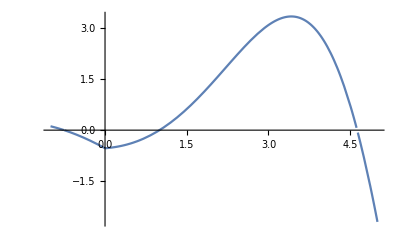

```mathematica
consts={vi[t_]:>UnitStep[t],l->1,r->1,c->1,C[_]->0};
Simplify@(vc/.sol1/.consts)[[1]][5]
Plot[((vc/.sol1/.consts)[[1]])[t],{t,-1,5}]
```

```mathematica
With[{context="p1`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Scratch Work

```mathematica
exportNotebookPDF[]
```

```mathematica
sys={v1[t]==v2[t],v1'[t]==5}
Reduce[Evaluate@sys,v1]
```

{v1[t]==v2[t],v1'[t]==5}

v1'[t]==5&&v1[t]==v2[t]